```mathematica
Clear[ rcap, scap ] ;
rcap = {Cos[#], Sin[#]} & ;
scap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
(*rcap[θ]
scap[θ, ϕ]*)

asz = 1.5 ;
toff = 0.1 ;
axes = Graphics3D[{
Black,
(*Red,*)Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
(*Blue,*)Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
(*Darker[Green, .8],*)Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;
```

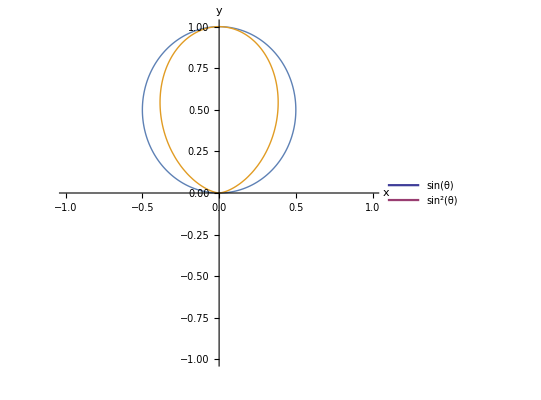

```mathematica
(*x1 = With[{funcList={Sin[t]rcap[t], Sin[t]^2rcap[t]},
labelList = {"sin(θ)", "sin^2(θ)"}
},With[{n=Length@funcList},Legended[ParametricPlot[funcList,{t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}],LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n]]
]*)
(*p1 = ParametricPlot[{Sin[t]rcap[t], Sin[t]^2rcap[t]}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}
,PlotLegends->Placed[{"sin(θ)", "sin^2(θ)"},{Right,Bottom}]
]*)
(*y1=With[{funcList={Sin[t] rcap[t],Sin[t]^2 rcap[t]},labelList={"sin(θ)", "sin^2(θ)"}},With[{n=Length@funcList},ParametricPlot[funcList,{t,0,Pi},PlotRange->{-1,1},AxesLabel->{x,y},PlotLegends->Placed[LineLegend[ColorData[1][#]&/@Range@n,labelList[[Range@n]]],{Right,Bottom}]]]]*)
(*http://mathematica.stackexchange.com/a/72045/10*)
SineAndSinSqFig3=With[{funcList={Sin[t] rcap[t],Sin[t]^2 rcap[t]},labelList={"sin(θ)", "sin^2(θ)"}},With[{n=Length@funcList},Legended[
ParametricPlot[funcList,{t,0,Pi},
PlotRange->{-1,1},
PlotStyle->Thick,
AxesLabel->{x,y}
],Placed[LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n,{Right,Bottom}]]]]
(*x1 = Plot[{Sin[t], Sin[t]^2}, {t, 0, Pi}, PlotRange -> {-1, 1}, AxesLabel -> {x, y}
,PlotLegends->Placed[{"sin(θ)", "sin^2(θ)"},{Right,Bottom}]
]*)
```

```mathematica
s1 = Show[axes,ParametricPlot3D[ {Sin[t]scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]]
```

-Graphics3D-

```mathematica
SineSq3D = Show[axes,
ParametricPlot3D[ {Sin[t]^2scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}
, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]
]
(*SphericalPlot3D[1+2 Cos[2 θ],{θ,0,Pi},{ϕ,0,2 Pi},Axes->False,PlotStyle->StippleShading[],PlotPoints->40,Mesh->None]*)
```

-Graphics3D-

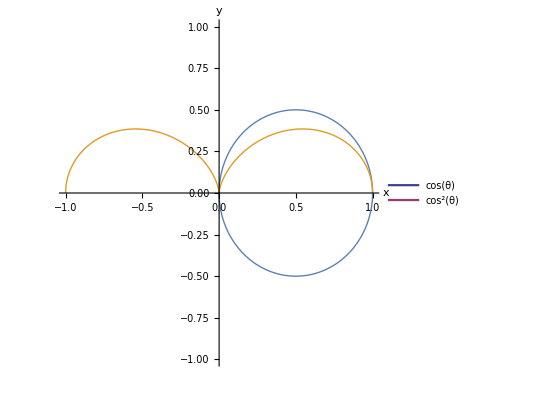

```mathematica
CoSineAndCoSineSqFig1=With[{funcList={Cos[t] rcap[t],Cos[t]^2 rcap[t]},labelList={"cos(θ)", "cos^2(θ)"}},With[{n=Length@funcList},Legended[
ParametricPlot[funcList,{t,0,Pi},
PlotRange->{-1,1},
PlotStyle->Thick,
AxesLabel->{x,y}
],Placed[LineLegend[(ColorData[1][#])&/@#,labelList[[#]]]&@Range@n,{Right,Bottom}]]]]
```

```mathematica
s3 = Show[axes,ParametricPlot3D[ {Cos[t]scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}
, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]]
```

-Graphics3D-

```mathematica
CoSineSq3D = Show[axes,ParametricPlot3D[ {Cos[t]^2scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}
, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]]
```

-Graphics3D-

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/ece1229-antenna" ]
```

/Users/pjoot/project/figures/ece1229-antenna

```mathematica
peeters`exportForLatex["SineAndSinSqFig3", SineAndSinSqFig3]
peeters`exportForLatex["CoSineAndCoSineSqFig1", CoSineAndCoSineSqFig1]
peeters`exportForLatex["SineSq3DFig4", SineSq3D]
peeters`exportForLatex["CoSineSq3DFig2", CoSineSq3D]
```

{SineAndSinSqFig3.eps,SineAndSinSqFig3pn.png}

{CoSineAndCoSineSqFig1.eps,CoSineAndCoSineSqFig1pn.png}

{SineSq3DFig4.eps,SineSq3DFig4pn.png}

{CoSineSq3DFig2.eps,CoSineSq3DFig2pn.png}

```mathematica
t1 = Show[axes,ParametricPlot3D[ { (Cos[t]^2 Cos[p]^2 + Sin[p]^2)scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]]
t2 = Show[axes,ParametricPlot3D[ { ((*Cos[t]^2 Cos[p]^2 +*) Sin[p]^2)scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]]
t3 = Show[axes,ParametricPlot3D[ { (Cos[t]^2 Cos[p]^2 (*+ Sin[p]^2*))scap[t, p]}, {t, 0, Pi}, {p, 0, 2 Pi}, AxesLabel -> {x, y, z}
,PlotStyle->HatchShading[0.6, Black]
,Lighting -> "Accent"
,PlotTheme->None
]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
peeters`exportForLatex["TaiAndPereiraSampleFieldThetaCapComponentFig1", t3]
peeters`exportForLatex["TaiAndPereiraSampleFieldPhiCapComponentFig2", t2]
peeters`exportForLatex["TaiAndPereiraSampleFieldAllComponentsFig3", t1]
```

{TaiAndPereiraSampleFieldThetaCapComponentFig1.eps,TaiAndPereiraSampleFieldThetaCapComponentFig1pn.png}

{TaiAndPereiraSampleFieldPhiCapComponentFig2.eps,TaiAndPereiraSampleFieldPhiCapComponentFig2pn.png}

{TaiAndPereiraSampleFieldAllComponentsFig3.eps,TaiAndPereiraSampleFieldAllComponentsFig3pn.png}